```mathematica
R=10000; (* X=R^2 *)
```

```mathematica
t=Flatten[Table[{i,j},{i,1,R},{j,0,Sqrt[R^2-i^2]}],1];
```

```mathematica
zone1angles=Table[N[ArcTan[(t[[i]][[2]])/(t[[i]][[1]])]],{i,1,Length[t]}];
```

```mathematica
angles=Sort[Join[N[zone1angles],N[zone1angles+Pi/2]]];
```

```mathematica
(*Export["2000AnglesList.mx",angles,"List"];*)
```

```mathematica
(*angles=Select[angles,0.25<=#<π/2+0.25 &];*)
```

```mathematica
Length[angles]
```

157079526

```mathematica
Variance2[l_]=Mean[l^2]-Mean[l]^2;
```

```mathematica
d=Table[{j,Divide[Variance2
[BinCounts[angles,{0.25,0.25+Pi/2,(π/2)/Round[R^(2*j)]}]],3/Pi *R^(2*(1-j))*Log[R]]},{j,0,1.5,0.05}];
```

```mathematica
d
```

{{0.,0.},{0.05,1.54413×10^-6},{0.1,3.55764×10^-6},{0.15,4.74424×10^-6},{0.2,4.39601×10^-6},{0.25,0.0000450577},{0.3,0.000304199},{0.35,0.000422654},{0.4,0.00108587},{0.45,0.0119893},{0.5,0.0204873},{0.55,0.130153},{0.6,0.241013},{0.65,0.33993},{0.7,0.438871},{0.75,0.537007},{0.8,0.634426},{0.85,0.728282},{0.9,0.816713},{0.95,0.895355},{1.,0.957915},{1.05,0.997742},{1.1,1.01455},{1.15,1.02124},{1.2,1.0239},{1.25,1.02496},{1.3,1.02538},{1.35,1.02555},{1.4,1.02562},{1.45,1.02565},{1.5,1.02562}}

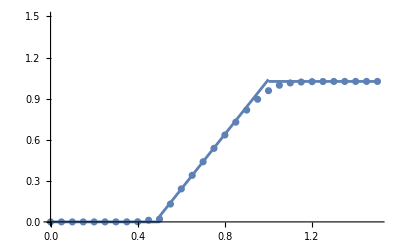

```mathematica
zeta2prime=π^2/6*(EulerGamma+Log[2]-12*Log[1.282427129]+Log[π]);
Lprime = (π/2)*(EulerGamma/2-Log[2]-2*Log[Abs[Gamma[1/4]/(2*π^(3/4))]]);
omega2=(3/π)*((3 EulerGamma)/2+(2/π)*Lprime-(6/π^2)*zeta2prime-1/2-π^2/12);
LowerOrd3=omega2/(3/π*Log[R]);
omega1:=(3/π)*((2/π)*(0.1929)-(6/π^2)*Zeta'[2]-2*Log[π]+EulerGamma/2+5/2-Pi^2/12);
LowerOrd2:=omega1/(3/π*Log[R]);
g1=Plot[0,{x,0,0.5}];
g2=Plot[2x-1+LowerOrd2,{x,0.5,1}];
g3=Plot[1+LowerOrd3,{x,1,1.5}];
Show[ListPlot[d],g1,g2,g3,PlotRange->{{0,1.5},{0,1.5}}]
```

```mathematica
(π/2)*(EulerGamma/2-Log[2]-2*Log[Abs[Gamma[1/4]/(2*π^(3/4))]])
```